Calculations from Garcia-Vidal (https://iopscience.iop.org/article/10.1088/1464-4258/7/2/013):

```mathematica
d=150*10^-9;
DutyCycle=0.533333;
h=160*10^-9;
a=(1-DutyCycle)*d;
c0=3*10^8;
```

```mathematica
S0[kx_]=Sqrt[a/d]*Sin[kx*a/2]/(kx*a/2);
```

```mathematica
ContourPlot[{kx^2-(w/c0)^2==(w/c0)^2*Tan[(w/c0)*h]^2*S0[kx]^4,w==c0*kx},{kx,0,(Pi/d)},{w,0,(Pi*c0/(2*h))},
LabelStyle->{Black},AspectRatio->1,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,20,FontFamily->"Cambria"],FrameLabel->{"k_x (m^-1)","ω"},FrameTicksStyle->Directive[Black,Thick,10,FontFamily->"Cambria"],ImageSize->250]
```

-Graphics-

Contour for k_x^2+k_y^2=1:

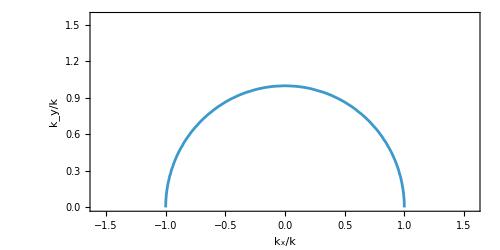

```mathematica
ContourPlot[{ky^2==1-kx^2},{kx,-(Pi/2),(Pi/2)},{ky,0,(Pi/2)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x/k","k_y/k"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500]
```

Contour for k_y=1-k_x^2/2 (Paraxial approx.):

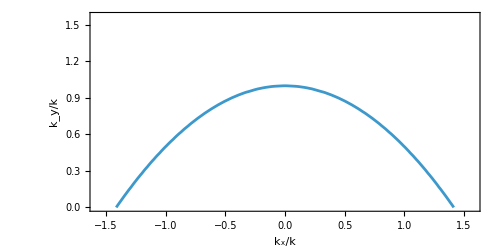

```mathematica
ContourPlot[{ky==1-kx^2/2},{kx,-(Pi/2),(Pi/2)},{ky,0,(Pi/2)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x/k","k_y/k"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500]
```

Contour of k_y=β_0+2 C_0 cos(k_x d) :

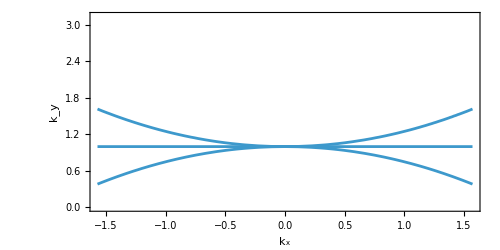

```mathematica
C0=1;
Show[ContourPlot[{ky==-Sqrt[1*kx^2+ky^2]+2 C0 Cos[kx*d]},{kx,-1*(Pi/2),1*(Pi/2)},{ky,0*(Pi/2),2*(Pi/2)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x","k_y"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],
ContourPlot[{ky==-Sqrt[0*kx^2+ky^2]+2 C0 Cos[kx*d]},{kx,-1*(Pi/2),1*(Pi/2)},{ky,0*(Pi/2),2*(Pi/2)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],
ContourPlot[{ky==-Sqrt[-1*kx^2+ky^2]+2 C0 Cos[kx*d]},{kx,-1*(Pi/2),1*(Pi/2)},{ky,0*(Pi/2),2*(Pi/2)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500]]
```

```mathematica
Λ=150;
Manipulate[ContourPlot[{2*Pi/λ==ky*(Pi/Λ)-2*(-0.05)*Cos[kx*(Pi/Λ)*Λ]},{kx,-1,1},{ky,-10,10},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x (π/a)","k_y"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,-10/Λ,-1/Λ},{λ,400,1200,10}]
```

Here we use t=(t_0/3)(λ-800) in β_0=k_y-2tcos(k_x Λ):
We can flip the dispersion by controlling λ:

```mathematica
Λ=150;
Manipulate[ContourPlot[{2*Pi/λ==ky-2*(t0/3*(λ-800))*Cos[kx*Λ]},{kx,-(Pi/Λ),(Pi/Λ)},{ky,-10*(Pi/Λ),10*(Pi/Λ)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x/λ","k_y/λ"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,0.01/Λ,0.1/Λ},{λ,400,1200,10}]
```

```mathematica
Λ=150;
Manipulate[
ContourPlot[{ω==ky-2*(t0/3*((2Pi/ω)-800))*Cos[kx*Λ]},{kx,-(Pi/Λ),(Pi/Λ)},{ω,0,0.02},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x","ω"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,0.001/Λ,0.01/Λ},{ky,0,1*(Pi/Λ)}]
```

```mathematica
Λ=150;
Manipulate[
ContourPlot[{ω==ky-2*(t0/3*((2Pi/ω)-800))*Cos[kx*Λ]},{ky,-10*(Pi/Λ),10*(Pi/Λ)},{ω,0,0.02},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_y","ω"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,0.0001/Λ,1/Λ},{kx,0,1*(Pi/Λ)}]
```

Here we use t=(t_0/3)(ω-2π/800) in β_0=k_y-2tcos(k_x Λ):
We can flip the dispersion by controlling ω:

```mathematica
Λ=150;
Manipulate[ContourPlot[{ω==ky-2*(t0/3)*Cos[kx*Λ]},{kx,-(Pi/Λ),(Pi/Λ)},{ky,-100*(Pi/Λ),100*(Pi/Λ)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x/λ","k_y/λ"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,1,50},{ω,0,3(Pi/Λ)}]
```

```mathematica
Λ=150;
Manipulate[ContourPlot[{ω==ky-2*(t0/3)*(ω-2Pi/800)*Cos[kx*Λ]},{kx,-(Pi/Λ),(Pi/Λ)},{ky,-10*(Pi/Λ),10*(Pi/Λ)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x/λ","k_y/λ"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,1,50},{ω,0,2(Pi/Λ)}]
```

```mathematica
Λ=150;
Manipulate[
ContourPlot[{ω==ky-2*(t0/3)*(ω-2Pi/800)*Cos[kx*Λ]},{kx,-(Pi/Λ),(Pi/Λ)},{ω,0,1(Pi/Λ)},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_x","ω"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,0,50},{ky,0,1*(Pi/Λ)}]
```

```mathematica
Solve[{ω==ky-2*(t0/3)*(ω-2Pi/800)*Cos[kx*Λ]},{ω}]
```

{{ω→(600 ky+π t0 Cos[150 kx])/(200 (3+2 t0 Cos[150 kx]))}}

```mathematica
Λ=150;
Manipulate[
ContourPlot[{ω==ky-2*(t0/3*(ω-2Pi/800))*Cos[kx*Λ]},{ky,-1*(Pi/Λ),1*(Pi/Λ)},{ω,0,Pi/Λ},
LabelStyle->{Black},AspectRatio->0.5,Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thick,Black,30,FontFamily->"Cambria"],FrameLabel->{"k_y","ω"},FrameTicksStyle->Directive[Black,Thick,20,FontFamily->"Cambria"],ImageSize->500],{t0,1,50},{kx,0,1*(Pi/Λ)}]
```